```mathematica
ReleaseHold[NotebookImport[NotebookDirectory[]<>"AllMatrices.nb","Input"]];
H1
H1//MatrixForm
```

{{m1+m2+mb,0,0,0,0},{0,m1+m2+mb,0,0,0},{0,0,1/(12 (m1+m2+mb))(l1^2 m1^2+4 l1^2 m1 m2+4 l2^2 m1 m2+l2^2 m2^2+4 l1^2 m1 mb+12 l1^2 m2 mb+4 l2^2 m2 mb+12 Ib (m1+m2+mb)+6 l1 l2 m2 (m1+2 mb) Cos[q2]),1/(12 (m1+m2+mb))(l2^2 m2 (4 m1+m2+4 mb)+l1^2 (m1^2+12 m2 mb+4 m1 (m2+mb))+6 l1 l2 m2 (m1+2 mb) Cos[q2]),(l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb))},{0,0,1/(12 (m1+m2+mb))(l2^2 m2 (4 m1+m2+4 mb)+l1^2 (m1^2+12 m2 mb+4 m1 (m2+mb))+6 l1 l2 m2 (m1+2 mb) Cos[q2]),1/(12 (m1+m2+mb))(l2^2 m2 (4 m1+m2+4 mb)+l1^2 (m1^2+12 m2 mb+4 m1 (m2+mb))+6 l1 l2 m2 (m1+2 mb) Cos[q2]),(l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb))},{0,0,(l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb)),(l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb)),(l2^2 m2 (4 m1+m2+4 mb))/(12 (m1+m2+mb))}}

(m1+m2+mb | 0 | 0 | 0 | 0
0 | m1+m2+mb | 0 | 0 | 0
0 | 0 | (l1^2 m1^2+4 l1^2 m1 m2+4 l2^2 m1 m2+l2^2 m2^2+4 l1^2 m1 mb+12 l1^2 m2 mb+4 l2^2 m2 mb+12 Ib (m1+m2+mb)+6 l1 l2 m2 (m1+2 mb) Cos[q2])/(12 (m1+m2+mb)) | (l2^2 m2 (4 m1+m2+4 mb)+l1^2 (m1^2+12 m2 mb+4 m1 (m2+mb))+6 l1 l2 m2 (m1+2 mb) Cos[q2])/(12 (m1+m2+mb)) | (l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb))
0 | 0 | (l2^2 m2 (4 m1+m2+4 mb)+l1^2 (m1^2+12 m2 mb+4 m1 (m2+mb))+6 l1 l2 m2 (m1+2 mb) Cos[q2])/(12 (m1+m2+mb)) | (l2^2 m2 (4 m1+m2+4 mb)+l1^2 (m1^2+12 m2 mb+4 m1 (m2+mb))+6 l1 l2 m2 (m1+2 mb) Cos[q2])/(12 (m1+m2+mb)) | (l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb))
0 | 0 | (l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb)) | (l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb)) | (l2^2 m2 (4 m1+m2+4 mb))/(12 (m1+m2+mb)))

```mathematica
Csc[ⅈ ]//N
```

0.-0.850918 ⅈ

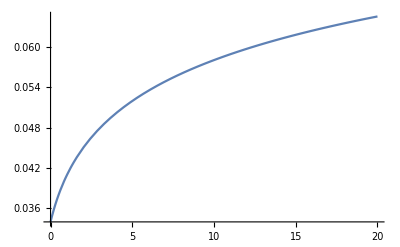

```mathematica
a=0.01;
b=30;
c=1;
Plot [a*Log[b*(c+t)],{t,0,20}]
```

```mathematica
ClearAll["Global`*"];
Clear[Derivative];
Remove["Global`*"];
Rot[axis_,angle_]:=Module[{},Switch[axis,`X,Return[{{1,0,0,0},{0,Cos[angle],-Sin[angle],0},{0,Sin[angle],Cos[angle],0},{0,0,0,1}}],`Y,Return[{{Cos[angle],0,Sin[angle],0},{0,1,0,0},{-Sin[angle],0,Cos[angle],0},{0,0,0,1}}],`Z,Return[{{Cos[angle],-Sin[angle],0,0},{Sin[angle],Cos[angle],0,0},{0,0,1,0},{0,0,0,1}}]];];

T[axis_,sh_]:=Module[{mac=IdentityMatrix[4]},Switch[axis,`X,mac[[1,4]]=sh,`Y,mac[[2,4]]=sh,`Z,mac[[3,4]]=sh];
Return[mac];];

res=T[X,a].Rot[Z,q1].T[Z,q2].T[X,Subscript[l, 2]].Rot[Y,q3].T[X,Subscript[l, 3]]//MatrixForm
```

(Cos[q1] Cos[q3] | -Sin[q1] | Cos[q1] Sin[q3] | a+Cos[q1] l_2+Cos[q1] Cos[q3] l_3
Cos[q3] Sin[q1] | Cos[q1] | Sin[q1] Sin[q3] | Sin[q1] l_2+Cos[q3] Sin[q1] l_3
-Sin[q3] | 0 | Cos[q3] | q2-Sin[q3] l_3
0 | 0 | 0 | 1)

```mathematica
Cos[o]Cos[p]-Sin[o]Sin[p]//Simplify
```

Cos[o+p]